## Calculations

```mathematica
Eigenvectors[{{fxx[x,y],fxy[x,y]},{fyx[x,y],fyy[x,y]}}]
```

{{-y/x,1},{x/y,1}}

### minimizer at origin

```mathematica
Limit[fx[x,y],{x,y}->{0,0}]
```

0

```mathematica
Limit[fy[x,y],{x,y}->{0,0}]
```

0

```mathematica
Simplify[Eigenvalues[{{fxx[x,y],fxy[x,y]},{fyx[x,y],fyy[x,y]}}]]
```

{(-1+ⅇ^(2 √(x^2+y^2)))/((1+ⅇ^(2 √(x^2+y^2))) √(x^2+y^2)),(4 ⅇ^(2 √(x^2+y^2)))/((1+ⅇ^(2 √(x^2+y^2)))^2)}

```mathematica
Limit[(-1+ⅇ^(2 √(x^2+y^2)))/((1+ⅇ^(2 √(x^2+y^2))) √(x^2+y^2)),{x,y}->{0,0}]
```

1

```mathematica
Limit[(4 ⅇ^(2 √(x^2+y^2)))/((1+ⅇ^(2 √(x^2+y^2)))^2),{x,y}->{0,0}]
```

1

## Lab 4 solutions

```mathematica
Off[General::spell]
Off[General::spell1]
Off[NMinimize::incst]
Clear[f]
nb=SelectedNotebook[ ];
inx=.4;
iny=.7;
fi=x^3-x y^2+y^3-y+1;
gi=0;
(*The next commands build partial derivatives that can be used in the iteration function (and an exact line search) while accepting current guesses in the argument later*)
fy[x_,y_]=D[f[x,y],y];
fx[x_,y_]=D[f[x,y],x];
fxx[x_,y_]=D[fx[x,y],x];
fxy[x_,y_]=D[fx[x,y],y];
fyx[x_,y_]=D[fy[x,y],x];
fyy[x_,y_]=D[fy[x,y],y];
PasteButton[Defer[fx[x,y]]];
PasteButton[Defer[fy[x,y]]];
PasteButton[Defer[fxx[x,y]]];
PasteButton[Defer[fxy[x,y]]];
PasteButton[Defer[fyx[x,y]]];
PasteButton[Defer[fyy[x,y]]];
(*The next command finds the exact line search step of f from {xo,yo} in the direction {d1,d2}*)
ExactStep[xo_,yo_,{d1_,d2_}]:=Module[{a,x,y,min},min=NMinimize[f[xo+a d1,yo+a d2],a];a/.min[[2]]]
(*The next command finds the solution to the SQP quadratic program with multiplier lam at (xo,yo)*)QP[xo_,yo_,lam_]:=Module[{L,TQ,x,y,min},L[x_,y_]:=f[x,y]-lam g[x,y];TQ[x_,y_]=L[xo,yo]+Derivative[1,0][L][xo,yo](x-xo)+Derivative[0,1][L][xo,yo](y-yo)+1/2{x-xo,y-yo}.{{Derivative[2,0][L][xo,yo],Derivative[1,1][L][xo,yo]},{Derivative[1,1][L][xo,yo],Derivative[0,2][L][xo,yo]}}.{x-xo,y-yo};min=Minimize[{TQ[x,y],g[xo,yo]+Derivative[1,0][g][xo,yo](x-xo)+Derivative[0,1][g][xo,yo](y-yo)≥0},{x,y}];{Replace[x,min[[2]]],Replace[y,min[[2]]]}]
(*The next command returns the new multiplier from the old lam associated with the old guess (xo,yo)*)QPlambda[lam_]:=Module[{L,x,y},L[x_,y_]:=f[x,y]-lam g[x,y];If[Chop[g[guess[[-2,1]],guess[[-2,2]]]+{Derivative[1,0][g][guess[[-2,1]],guess[[-2,2]]],Derivative[0,1][g][guess[[-2,1]],guess[[-2,2]]]}.{guess[[-1,1]]-guess[[-2,1]],guess[[-1,2]]-guess[[-2,2]]}]==0 ,If[ Derivative[0,1][g][guess[[-2,1]],guess[[-2,2]]]≠0,(Derivative[0,1][L][guess[[-2,1]],guess[[-2,2]]]+(guess[[-1,2]]-guess[[-2,2]]) Derivative[0,2][L][guess[[-2,1]],guess[[-2,2]]]+(guess[[-1,1]]-guess[[-2,1]]) Derivative[1,1][L][guess[[-2,1]],guess[[-2,2]]])/(Derivative[0,1][g][guess[[-2,1]],guess[[-2,2]]]),If[ Derivative[1,0][g][guess[[-2,1]],guess[[-2,2]]]≠0,(Derivative[1,0][L][guess[[-2,1]],guess[[-2,2]]]+(guess[[-1,1]]-guess[[-2,1]]) Derivative[2,0][L][guess[[-2,1]],guess[[-2,2]]]+(guess[[-1,2]]-guess[[-2,2]]) Derivative[1,1][L][guess[[-2,1]],guess[[-2,2]]])/(Derivative[1,0][g][guess[[-2,1]],guess[[-2,2]]]),0]],0]]
(*The next command iterates the iteration function once and updates the list of guesses*)
IterateOpt[{xo_,yo_}]:=Module[{xn,yn},{xn,yn}=Evaluate[G[xo,yo]];guess=AppendTo[guess,N[{xn,yn}]];]
(*The next command draws the contour plot of the objective with the guesslist and constraint curve--if there is one--overlayed*)
VisualOpt[list_]:=Module[{xmax,xmin,ymax,ymin},xmax=Max[list[[All,1]]];xmin=Min[list[[All,1]]];ymax=Max[list[[All,2]]];ymin=Min[list[[All,2]]];
Grid[{{Grid[{{"newest 20 guesses"},{If[Length[list]≤19,TableForm[list],TableForm[Take[list,-20]]]}},Alignment->{Center,Center}],Show[ContourPlot[fi,{x,xmin-If[xmax==xmin,1,(xmax-xmin)]/10,xmax+If[xmax==xmin,1,(xmax-xmin)]/10},{y,ymin-If[ymax==ymin,1,(ymax-ymin)]/10,ymax+If[ymax==ymin,1,(ymax-ymin)]/10},Contours->20,PlotPoints->25],Graphics[{Blue,Line[list]}],
Graphics[{Blue,PointSize[Medium],Point[list]}],Graphics[{Blue,PointSize[Large],Point[First[list]]}],Graphics[{Red,PointSize[Large],Point[Last[list]]}],RegionPlot[gi<0,{x,xmin-If[xmax==xmin,1,(xmax-xmin)]/10,xmax+If[xmax==xmin,1,(xmax-xmin)]/10},{y,ymin-If[ymax==ymin,1,(ymax-ymin)]/10,ymax+If[ymax==ymin,1,(ymax-ymin)]/10},PlotStyle->Opacity[.3]],ContourPlot[gi,{x,xmin-If[xmax==xmin,1,(xmax-xmin)]/10,xmax+If[xmax==xmin,1,(xmax-xmin)]/10},{y,ymin-If[ymax==ymin,1,(ymax-ymin)]/10,ymax+If[ymax==ymin,1,(ymax-ymin)]/10},Contours->{0},PlotPoints->25,ContourShading->False,ContourStyle->{Thick,Blue}],Frame->True,FrameLabel->{Style["Newest guess is "Style[Last[list],Red],Medium],,Style["First guess is "Style[First[list],Blue],Medium]},ImageSize->Medium]}},ItemSize->{{15,30}},Alignment->{Center,Top},Frame->All]]
(*The next command makes a pop-up box to intiialize the method*)
Start:=Module[{},DialogInput[{Grid[{{TextCell["First Guess"]},{Grid[{{TextCell["x ="],InputField[Dynamic[inx],Number,ImageSize->30],TextCell["y ="],InputField[Dynamic[iny],Number,ImageSize->30]}}]}}],Grid[{{TextCell["Objective function"]},{TextCell["f[x,y]"],InputField[Dynamic[fi]]}}],Grid[{{TextCell["Constraint function"]},{TextCell["g[x,y]"],InputField[Dynamic[gi]],TextCell["≥ 0"]}}],
DefaultButton["Done",DialogReturn[guess={{inx,iny}};f[x_,y_]=fi;g[x_,y_]=gi;]]}]];
```

```mathematica
Start
```

```mathematica
f[x_,y_]=Log[1+ⅇ^(2 √(x^2+y^2))]-√(x^2+y^2);
inx=.7;
iny=.7;

inx=.8;
iny=.8;
```

## Building the Method

```mathematica
G[x_,y_]:={x,y}-Inverse[{{fxx[x,y],fxy[x,y]},{fyx[x,y],fyy[x,y]}}].{fx[x,y],fy[x,y]}
```

## Computing Guesses

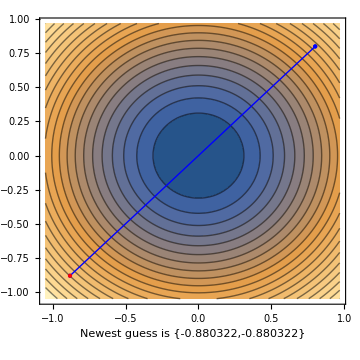
newest 20 guesses
0.8 | 0.8
-0.880322 | -0.880322 | -Graphics-

```mathematica
IterateOpt[Last[guess]];Print[VisualOpt[guess]]
```

### 1.(a)

```mathematica
TableForm[guess]
```

0.7 | 0.7
-0.555809 | -0.555809
0.258949 | 0.258949
-0.0237807 | -0.0237807
0.0000179353 | 0.0000179353
-7.607×10^-15 | -7.56123×10^-15
1.86939×10^-16 | 7.75446×10^-17

### 1.(b)

```mathematica
fx[guess[[-1,1]],guess[[-1,2]]]
```

2.22045×10^-16

```mathematica
fy[guess[[-1,1]],guess[[-1,2]]]
```

1.11022×10^-16

### 1.(c)

```mathematica
Eigenvalues[{{fxx[guess[[-1,1]],guess[[-1,2]]],fxy[guess[[-1,1]],guess[[-1,2]]]},{fyx[guess[[-1,1]],guess[[-1,2]]],fyy[guess[[-1,1]],guess[[-1,2]]]}}]
```

{1.19275,0.682253}

### 1.(d)

```mathematica
TableForm[guess]
```

0.8 | 0.8
-0.880322 | -0.880322
1.23701 | 1.23701
-4.60469 | -4.60469
80106.1 | 80106.1
-2.24069×10^15 | -2.24069×10^15

### 2.

```mathematica
Simplify[Eigenvalues[{{fxx[x,y],fxy[x,y]},{fyx[x,y],fyy[x,y]}}]]
```

{(-1+ⅇ^(2 √(x^2+y^2)))/((1+ⅇ^(2 √(x^2+y^2))) √(x^2+y^2)),(4 ⅇ^(2 √(x^2+y^2)))/((1+ⅇ^(2 √(x^2+y^2)))^2)}

```mathematica
Plot3D[(4 ⅇ^(2 √(x^2+y^2)))/((1+ⅇ^(2 √(x^2+y^2)))^2),{x,-10,10},{y,-10,10},PlotRange->{0,1}]
```

-Graphics3D-

### 3.

```mathematica
Simplify[{fx[x,y],fy[x,y]}]
```

{((-1+ⅇ^(2 √(x^2+y^2))) x)/((1+ⅇ^(2 √(x^2+y^2))) √(x^2+y^2)),((-1+ⅇ^(2 √(x^2+y^2))) y)/((1+ⅇ^(2 √(x^2+y^2))) √(x^2+y^2))}

### 4.

Since the gradient is a multiple c of the position vector (which is an eigenvector for the inverse second-derivative matrix), we know from the matrix equation defining eigenvalues that the inverse second-derivative matrix applied to the gradient is the same as α(x,y)=1/ϵ(x,y) applied to the gradient.  

This means that Newton’s update in this case is simply {x,y}-α(x,y){fx[x,y],fy[x,y]}, which is the same update as steepest-descent with step-factor α(x,y).

### 5.

Newton’s optimization method in this case behaves like steepest-descent with a very large (and increasing) step-factor once the guesses grow large.  We generally design step-factors to ensure good behavior in steepest-descent (e.g., actual descent), but these step-factors do not necessarily have that effect (nor were they designed to).  The initial guess (0.8,0.8) is apparently just large enough to be in the domain where magnified step-factors begin to occur.    Notice that the guesses in part 1(d) jump back and forth across the origin, since the negative gradients always point toward the origin.  Depending on your version of Mathematica, you may not observe this behavior (nearly zero ϵ(x,y) may be calculated as negative numbers, which will flip the direction of the next guess).